## First define the genrator base

```mathematica
allGeneratorVariables3=Sort[Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs3[k,"graph"]]]},
allGraphs3[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs3GeneratorAtomKeys}
],CompareSymbols];
```

```mathematica
repFullToGen=ToRules[
Reduce[
Table[
allGraphs3[k,"colofourgenerator"]==allGraphs3[k,"colofour"]
,
{k,allGraphs3GeneratorAtomKeys}
],
Table[allGraphs3[k,"colofour"],{k,allGraphs3AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs3[k,"colofourgenerator"]=Simplify[allGraphs3[k,"colofour"]/.repFullToGen],
{k,Sort[Keys[allGraphs3]]}
],k];
```

## Now define the base basic data

```mathematica
Bases3=Association[];
```

```mathematica
Bases3["C"]=Association[];
```

```mathematica
Bases3["C","Colofour"]="colofour";
```

```mathematica
Bases3["E"]=Association[];
```

```mathematica
Bases3["E","Colofour"]="colofourrealnull";
```

```mathematica
Bases3["G"]=Association[];
```

```mathematica
Bases3["G","Colofour"]="colofourgenerator";
```

```mathematica
allBases3={"C","E","G"}
```

{C,E,G}

## Compute keys and variables

```mathematica
Table[Bases3[base,"AtomKeys"]=Sort[Select[Keys[allGraphs3],Length[ListofVars[allGraphs3[#,Bases3[base,"Colofour"]]]]==1&],CompareSymbols[allGraphs3[#1,Bases3[base,"Colofour"]],allGraphs3[#2,Bases3[base,"Colofour"]]]&]
,{base,allBases3}];
```

```mathematica
Table[Bases3[base,"Variables"]=Table[allGraphs3[k,Bases3[base,"Colofour"]],{k,Bases3[base,"AtomKeys"]}]
,{base,allBases3}];
```

```mathematica
BaseCoeff3[key_,base_]:=Table[Coefficient[allGraphs3[key,Bases3[base,"Colofour"]],var],{var,Bases3[base,"Variables"]}]
```

```mathematica
BaseCoeff3[0,"E"]
```

{1,0,0,0,0}

```mathematica
ConversionMatrix3[base1_,base2_]:=Table[BaseCoeff3[key1,base2],{key1,Bases3[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases3[base,"AtomKeys"],{base,allBases3}]//Flatten//DeleteDuplicates//Length
```

12

```mathematica
32
```

32

## Checking some conversion matrix identities

```mathematica
ConversionMatrix3["E","C"]==Transpose[ConversionMatrix3["G","C"]]
```

True

```mathematica
ConversionMatrix3["E","C"]==Inverse[ConversionMatrix3["C","E"]]
```

True

```mathematica
ConversionMatrix3["G","C"]==Transpose[Inverse[ConversionMatrix3["C","E"]]]
```

True

```mathematica
Table[base->ConversionMatrix3[base,base]==IdentityMatrix[5],{base,allBases3}]
```

{C→True,E→True,G→True}

## Viewing come COnversion matrcxes

```mathematica
Table[Det[ConversionMatrix3[base1,base2]],{base1,allBases3},{base2,allBases3}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
Table[base1->Eigenvalues[ConversionMatrix3[base1,base2]]//N,{base1,allBases3},{base2,{"G"}}]
```

```mathematica
{{"C"->{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}},{"E"->{0.+2.805883701475779 ⅈ,0.-2.805883701475779 ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.+1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,0.-1. ⅈ,1.,0.+0.35639395869260033 ⅈ,0.-0.35639395869260033 ⅈ}},{"G"->{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}
```

```mathematica
Table[base1->Det[ConversionMatrix3[base1,base2]],{base1,allBases3},{base2,{"G"}}]
```

{{C→1},{E→1},{G→1}}

```mathematica
Tally[Table[Sort[Map[Length,allGraphs3[k,"vertexsets"]]],{k,allGraphs3AtomKeys}]]
```

```mathematica
{{{1,1,1,1},1},{{1,1,2},6},{{1,3},3},{{2,2},3},{{3},1}}
```

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix3[base1,base2],ImageSize->130],{base1,allBases3},{base2,allBases3}],TableHeadings->{allBases3, allBases3},TableAlignments->{Center, Center}]
```

| C | E | G
C | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics-

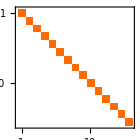
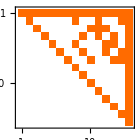
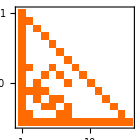
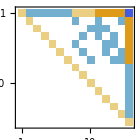
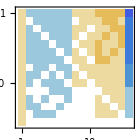
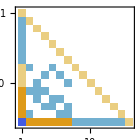
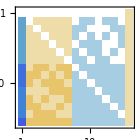
| G | E | C
G | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics-
C | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[Inverse[ConversionMatrix3[base1,base2]],ImageSize->130],{base1,allBases3},{base2,allBases3}],TableHeadings->{Reverse[allBases3], Reverse[allBases3]},TableAlignments->{Center, Center}]
```

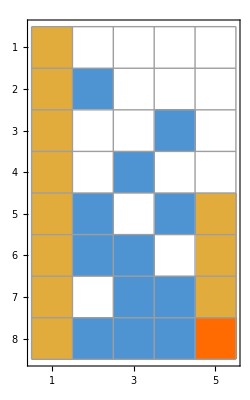

```mathematica
MatrixPlot[Sort[Table[BaseCoeff3[k,"E"],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}],Total[Abs[#2]]>Total[Abs[#1]]&],Mesh->All]
```

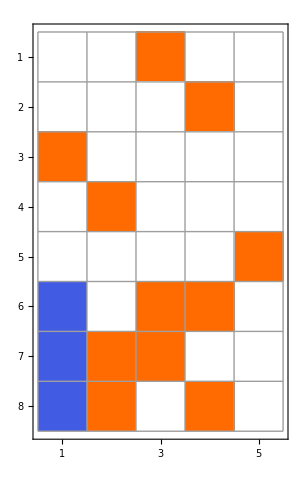
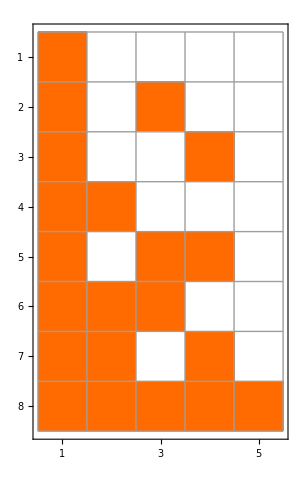

```mathematica
Row[{
MatrixPlot[Sort[Table[BaseCoeff3[k,"G"],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}],Total[Abs[#2]]>Total[Abs[#1]]&],Mesh->All,ImageSize->300],
MatrixPlot[Sort[Table[BaseCoeff3[k,"C"],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}],Total[Abs[#2]]>Total[Abs[#1]]&],Mesh->All,ImageSize->300]
},ImageSize->1200]
```

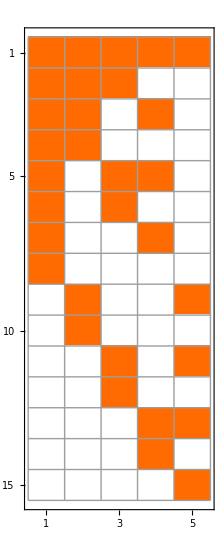

```mathematica
Rotate[MatrixPlot[Sort[Table[BaseCoeff3[k,"C"],{k,Keys[allGraphs3]}],FromDigits[#1,2]>FromDigits[#2,2]&],Mesh->All],Pi/2]
```